# Density Profiles

## Γ = 1 and K = 1

```mathematica
(*We chose to solve the simpliest case first. We take the Generalised Equation for Γ and K = 1 and use a numerical differential solver to find an interpolating function for m'[r]*)
```

```mathematica
ClearAll[m]
```

```mathematica
mp1=NDSolveValue[{-16 π^2 m'[r] (6 (3 m[r]+r (-1+m'[r])) m'[r]+r (3 r+r^3 Λ-6 m[r]) m''[r])==0/.Λ->10^-52,m[0.001]==10^-5,m[9000]==0.1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

```mathematica
(*Above is the stored interpolating function mp1[r]. Now using the relationship ρ = m'/(4 πr^2), we can plot the stored function as a density profile rather than a mass profile.*)
```

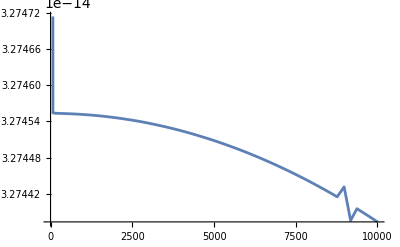

```mathematica
Plot[mp1[r]/(4 π r^2),{r,0,10000}]
```

## K = r and Γ = 1

```mathematica
(*We can take the generalised equation and set whatever conditions we would like on the parameters. Below we took one of the equations and set K = r instead of 1*)
```

```mathematica
FullSimplify[(m'[r]^2 (-16^Γ[r] π^(2 Γ[r]) (r^3 Λ+3 m[r])-3 (4 π)^(1+Γ[r]) r^3 K[r] (m'[r]/r^2)^Γ[r])-4 π r^4 (m'[r]/r^2)^(1+Γ[r]) (r ((4 π)^Γ[r] r (3+r^2 Λ)-3 2^(1+2 Γ[r]) π^Γ[r] m[r]) K'[r]+12 π r^3 K[r]^2 (m'[r]/r^2)^Γ[r]+K[r] ((4 π)^Γ[r] (r^3 Λ+3 m[r]+r^2 (3+r^2 Λ) Log[m'[r]/(π r^2)] Γ'[r])-2^(1+2 Γ[r]) π^Γ[r] ((3 r+r^3 Λ-6 m[r]) Γ[r]+r (r^3 Λ Log[2]+r Log[8]+3 Log[m'[r]/(4 π r^2)] m[r]) Γ'[r])))-4 π r^3 K[r] ((4 π)^Γ[r] r (3+r^2 Λ)-3 2^(1+2 Γ[r]) π^Γ[r] m[r]) Γ[r] (m'[r]/r^2)^Γ[r] m''[r])/.{K[r]->r,K'[r]->1,Γ[r]->1,Γ'[r]->0}]
```

-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r])

```mathematica
(*We can now take this equation above and use the numerical differential solver to find an interpolating funtion for m'[r] and use the same relationship as before to make a density profile*)
```

```mathematica
mp2=NDSolveValue[{-16 π^2 m'[r] ((r^2 (-3+r Λ)+(3+9 r) m[r]) m'[r]+3 r^2 (1+r) m'[r]^2+r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52},m[0.001]==10^-5,m[9000]==1},m',{r,0.0001,9000}]
```

InterpolatingFunction[…]

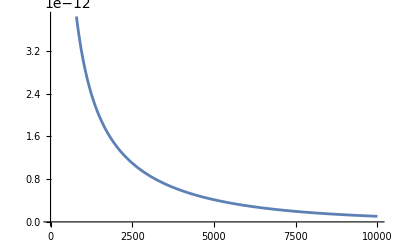

```mathematica
Plot[mp2[r]/(4 π r^2),{r,0.1,10000}]
```

## K = r/b and Γ = 1

```mathematica
FullSimplify[(m'[r]^2 (-16^Γ[r] π^(2 Γ[r]) (r^3 Λ+3 m[r])-3 (4 π)^(1+Γ[r]) r^3 K[r] (m'[r]/r^2)^Γ[r])-4 π r^4 (m'[r]/r^2)^(1+Γ[r]) (r ((4 π)^Γ[r] r (3+r^2 Λ)-3 2^(1+2 Γ[r]) π^Γ[r] m[r]) K'[r]+12 π r^3 K[r]^2 (m'[r]/r^2)^Γ[r]+K[r] ((4 π)^Γ[r] (r^3 Λ+3 m[r]+r^2 (3+r^2 Λ) Log[m'[r]/(π r^2)] Γ'[r])-2^(1+2 Γ[r]) π^Γ[r] ((3 r+r^3 Λ-6 m[r]) Γ[r]+r (r^3 Λ Log[2]+r Log[8]+3 Log[m'[r]/(4 π r^2)] m[r]) Γ'[r])))-4 π r^3 K[r] ((4 π)^Γ[r] r (3+r^2 Λ)-3 2^(1+2 Γ[r]) π^Γ[r] m[r]) Γ[r] (m'[r]/r^2)^Γ[r] m''[r])/.{K[r]->r/b,K'[r]->1/b,Γ[r]->1,Γ'[r]->0}]
```

-(16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r]))/b^2

```mathematica
mp3=NDSolveValue[{-1/b^2 16 π^2 m'[r] (b (r^2 (-3+b r Λ)+3 (b+3 r) m[r]) m'[r]+3 r^2 (b+r) m'[r]^2+b r^2 (3 r+r^3 Λ-6 m[r]) m''[r])==0/.{Λ->10^-52,b->10000},m[0.001]==0,m[9000]==1},m',{r,0.0001,10000}]
```

InterpolatingFunction[…]

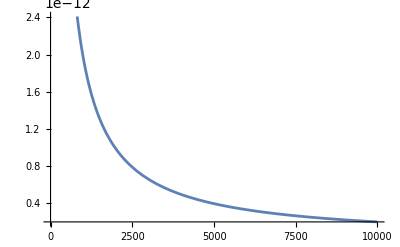

```mathematica
Plot[mp3[r]/(4 π r^2),{r,0,10000}]
```

# Γ Profiles

```mathematica
(*Γ = r, K = 1*)
```

## K = 1 and ρ = ρ_0

```mathematica
(*Using the relationship m[r] = 4/3 ρπr^3, m'[r] = 4 ρπr^2, and m''[r]= 8ρπr. We can rewrite our equations into density distributions instead of mass distributions*)
```

```mathematica
FullSimplify[m'[r]^2 (-16^Γ[r] π^(2 Γ[r]) (r^3 Λ+3 m[r])-3 K (4 π)^(1+Γ[r]) r^3 (m'[r]/r^2)^Γ[r])-4 K π r^4 (m'[r]/r^2)^(1+Γ[r]) (12 K π r^3 (m'[r]/r^2)^Γ[r]-2^(1+2 Γ[r]) π^Γ[r] ((3 r+r^3 Λ-6 m[r]) Γ[r]+r (r^3 Λ Log[2]+r Log[8]+3 Log[m'[r]/(4 π r^2)] m[r]) Γ'[r])+(4 π)^Γ[r] (3 m[r]+r^2 (r Λ+(3+r^2 Λ) Log[m'[r]/(π r^2)] Γ'[r])))-4 K π r^3 ((4 π)^Γ[r] r (3+r^2 Λ)-3 2^(1+2 Γ[r]) π^Γ[r] m[r]) Γ[r] (m'[r]/r^2)^Γ[r] m''[r]/.{K->1,m[r]->4/3 ρ[r]π r^3,m'[r]->4 ρ[r]π r^2,m''[r]->8 ρ[r] π r}]
```

-16 π^2 r^6 ρ[r] (3 (4 π)^(1+2 Γ[r]) r ρ[r]^(2 Γ[r])+r ρ[r] (16^Γ[r] π^(2 Γ[r]) Λ+(4 π)^(1+2 Γ[r]) ρ[r])+16^Γ[r] π^(2 Γ[r]) ρ[r]^Γ[r] (r (Λ+16 π ρ[r])+Log[ρ[r]] (3+r^2 Λ-8 π r^2 ρ[r]) Γ'[r]))

```mathematica
(*We took the master equation and set K[r] = 1, K'[r] = 0, and converted mass into density)*)
```

```mathematica
(*For this specific case we are taking ρ[r] to be uniform or just some contant value. This means our ρ[r] turns into Subscript[ρ, 0]*)
```

```mathematica
FullSimplify[-16 π^2 r^6 ρ[r] (3 (4 π)^(1+2 Γ[r]) r ρ[r]^(2 Γ[r])+r ρ[r] (16^Γ[r] π^(2 Γ[r]) Λ+(4 π)^(1+2 Γ[r]) ρ[r])+16^Γ[r] π^(2 Γ[r]) ρ[r]^Γ[r] (r (Λ+16 π ρ[r])+Log[ρ[r]] (3+r^2 Λ-8 π r^2 ρ[r]) Γ'[r]))/.{ρ[r]->Subscript[ρ, 0]}]
```

-16 π^2 r^6 ρ_0 (3 (4 π)^(1+2 Γ[r]) r ρ_0^(2 Γ[r])+r ρ_0 (16^Γ[r] π^(2 Γ[r]) Λ+(4 π)^(1+2 Γ[r]) ρ_0)+16^Γ[r] π^(2 Γ[r]) ρ_0^Γ[r] (r (Λ+16 π ρ_0)+Log[ρ_0] (3+r^2 Λ-8 π r^2 ρ_0) Γ'[r]))

```mathematica
(*We can now find how Γ[r] changes*)
```

```mathematica
gd1=NDSolveValue[{(3 (4 π)^(1+2 Γ[r]) r Subscript[ρ, 0]^(2 Γ[r])+r Subscript[ρ, 0] (16^Γ[r] π^(2 Γ[r]) Λ+(4 π)^(1+2 Γ[r]) Subscript[ρ, 0])+16^Γ[r] π^(2 Γ[r]) Subscript[ρ, 0]^Γ[r] (r (Λ+16 π Subscript[ρ, 0])+Log[Subscript[ρ, 0]] (3+r^2 Λ-8 π r^2 Subscript[ρ, 0]) Γ'[r]))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

InterpolatingFunction[…]

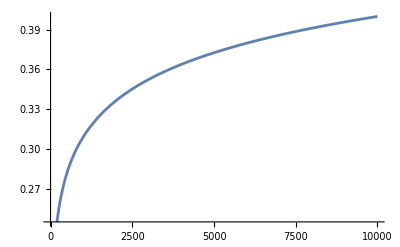

```mathematica
Plot[gd1[r],{r,0,10000}]
```

## K = 1 and ρ = ρ_0(1-r/b)

```mathematica
(*Here we will start with the same equation used at the beginning of the last section with the only difference being our what ρ is a function of*)
```

```mathematica
FullSimplify[m'[r]^2 (-16^Γ[r] π^(2 Γ[r]) (r^3 Λ+3 m[r])-3 K (4 π)^(1+Γ[r]) r^3 (m'[r]/r^2)^Γ[r])-4 K π r^4 (m'[r]/r^2)^(1+Γ[r]) (12 K π r^3 (m'[r]/r^2)^Γ[r]-2^(1+2 Γ[r]) π^Γ[r] ((3 r+r^3 Λ-6 m[r]) Γ[r]+r (r^3 Λ Log[2]+r Log[8]+3 Log[m'[r]/(4 π r^2)] m[r]) Γ'[r])+(4 π)^Γ[r] (3 m[r]+r^2 (r Λ+(3+r^2 Λ) Log[m'[r]/(π r^2)] Γ'[r])))-4 K π r^3 ((4 π)^Γ[r] r (3+r^2 Λ)-3 2^(1+2 Γ[r]) π^Γ[r] m[r]) Γ[r] (m'[r]/r^2)^Γ[r] m''[r]/.{K->1,m[r]->4 Subscript[ρ, 0] π (r^3/3-r^4/(4 b)),m'[r]->4 Subscript[ρ, 0] π (r^2-r^3/b),m''[r]->4 Subscript[ρ, 0] π (2 r-(3 r^2)/b)}]
```

1/b^3 16 π^2 r^6 ρ_0 (16^Γ[r] π^(1+2 Γ[r]) (b-r)^2 r (-4 b+3 r) ρ_0^2+b^2 (((b-r) ρ_0)/b)^Γ[r] (16^Γ[r] π^(2 Γ[r]) (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (r (Λ+12 π (((b-r) ρ_0)/b)^Γ[r])+(3+r^2 Λ) Log[((b-r) ρ_0)/b] Γ'[r]))+16^Γ[r] b π^(2 Γ[r]) r ρ_0 (-(b-r)^2 Λ+π (((b-r) ρ_0)/b)^Γ[r] (-((16 b-15 r) (b-r))+2 r (-4 b+3 r) (Γ[r]+(-b+r) Log[((b-r) ρ_0)/b] Γ'[r]))))

```mathematica
gd2=NDSolveValue[{(16^Γ[r] π^(1+2 Γ[r]) (b-r)^2 r (-4 b+3 r) Subscript[ρ, 0]^2+b^2 (((b-r) Subscript[ρ, 0])/b)^Γ[r] (16^Γ[r] π^(2 Γ[r]) (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (r (Λ+12 π (((b-r) Subscript[ρ, 0])/b)^Γ[r])+(3+r^2 Λ) Log[((b-r) Subscript[ρ, 0])/b] Γ'[r]))+16^Γ[r] b π^(2 Γ[r]) r Subscript[ρ, 0] (-(b-r)^2 Λ+π (((b-r) Subscript[ρ, 0])/b)^Γ[r] (-((16 b-15 r) (b-r))+2 r (-4 b+3 r) (Γ[r]+(-b+r) Log[((b-r) Subscript[ρ, 0])/b] Γ'[r]))))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

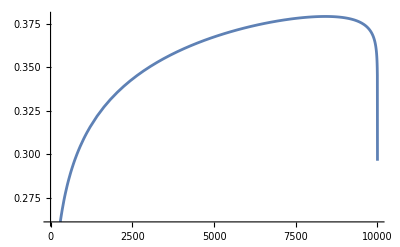

```mathematica
Plot[gd2[r],{r,0,10000}]
```

## K = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
FullSimplify[m'[r]^2 (-16^Γ[r] π^(2 Γ[r]) (r^3 Λ+3 m[r])-3 K (4 π)^(1+Γ[r]) r^3 (m'[r]/r^2)^Γ[r])-4 K π r^4 (m'[r]/r^2)^(1+Γ[r]) (12 K π r^3 (m'[r]/r^2)^Γ[r]-2^(1+2 Γ[r]) π^Γ[r] ((3 r+r^3 Λ-6 m[r]) Γ[r]+r (r^3 Λ Log[2]+r Log[8]+3 Log[m'[r]/(4 π r^2)] m[r]) Γ'[r])+(4 π)^Γ[r] (3 m[r]+r^2 (r Λ+(3+r^2 Λ) Log[m'[r]/(π r^2)] Γ'[r])))-4 K π r^3 ((4 π)^Γ[r] r (3+r^2 Λ)-3 2^(1+2 Γ[r]) π^Γ[r] m[r]) Γ[r] (m'[r]/r^2)^Γ[r] m''[r]/.{K->1,m[r]->4 Subscript[ρ, 0] π (r^3/3-r^5/(5 b^2)),m'[r]->4 Subscript[ρ, 0] π (r^2-r^4/b^2),m''[r]->4 Subscript[ρ, 0] π (2 r-(4 r^3)/b^2)}]
```

1/(5 b^6)16 π^2 r^6 ρ_0 ((4 π)^(1+2 Γ[r]) r (b^2-r^2)^2 (-5 b^2+3 r^2) ρ_0^2+16^Γ[r] b^2 π^(2 Γ[r]) r ρ_0 (-5 (b^2-r^2)^2 Λ+8 π ((1-r^2/b^2) ρ_0)^Γ[r] (-10 b^4+19 b^2 r^2-9 r^4+(-10 b^2 r^2+6 r^4) Γ[r]+r (5 b^4-8 b^2 r^2+3 r^4) Log[(1-r^2/b^2) ρ_0] Γ'[r]))+5 b^4 ((1-r^2/b^2) ρ_0)^Γ[r] (2^(1+4 Γ[r]) π^(2 Γ[r]) r (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (b+r) (r (Λ+12 π ((1-r^2/b^2) ρ_0)^Γ[r])+(3+r^2 Λ) Log[(1-r^2/b^2) ρ_0] Γ'[r])))

```mathematica
gd3=NDSolveValue[{((4 π)^(1+2 Γ[r]) r (b^2-r^2)^2 (-5 b^2+3 r^2) Subscript[ρ, 0]^2+16^Γ[r] b^2 π^(2 Γ[r]) r Subscript[ρ, 0] (-5 (b^2-r^2)^2 Λ+8 π ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r] (-10 b^4+19 b^2 r^2-9 r^4+(-10 b^2 r^2+6 r^4) Γ[r]+r (5 b^4-8 b^2 r^2+3 r^4) Log[(1-r^2/b^2) Subscript[ρ, 0]] Γ'[r]))+5 b^4 ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r] (2^(1+4 Γ[r]) π^(2 Γ[r]) r (3+r^2 Λ) Γ[r]-(4 π)^(2 Γ[r]) (b-r) (b+r) (r (Λ+12 π ((1-r^2/b^2) Subscript[ρ, 0])^Γ[r])+(3+r^2 Λ) Log[(1-r^2/b^2) Subscript[ρ, 0]] Γ'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},Γ[0.001]==0.0001},Γ,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

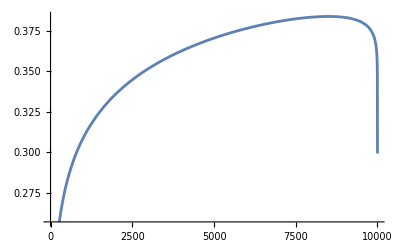

```mathematica
Plot[gd3[r],{r,0,10000}]
```

# K Plots

## Γ = 1 and ρ = ρ_0

```mathematica
(*The steps for this section is the same as the prior sections but instead of getting functions for Γ we are finding functions for K*)
```

```mathematica
FullSimplify[m'[r]^2 (-16^Γ π^(2 Γ) (r^3 Λ+3 m[r])-3 (4 π)^(1+Γ) r^3 K[r] (m'[r]/r^2)^Γ)-4 π r^4 (m'[r]/r^2)^(1+Γ) (K[r] (-2^(1+2 Γ) π^Γ Γ (3 r+r^3 Λ-6 m[r])+(4 π)^Γ (r^3 Λ+3 m[r]))+r ((4 π)^Γ r (3+r^2 Λ)-3 2^(1+2 Γ) π^Γ m[r]) K'[r]+12 π r^3 K[r]^2 (m'[r]/r^2)^Γ)-4 π r^3 Γ K[r] ((4 π)^Γ r (3+r^2 Λ)-3 2^(1+2 Γ) π^Γ m[r]) (m'[r]/r^2)^Γ m''[r]/.{Γ->1,m[r]->4/3 Subscript[ρ, 0] π r^3,m'[r]->4 Subscript[ρ, 0] π r^2,m''[r]->8 Subscript[ρ, 0] π r}]
```

256 π^4 r^6 ρ_0^2 (-r (1+K[r]) (Λ+4 (π+3 π K[r]) ρ_0)-(3+r^2 Λ-8 π r^2 ρ_0) K'[r])

```mathematica
kd1=NDSolveValue[{(-r (1+K[r]) (Λ+4 (π+3 π K[r]) Subscript[ρ, 0])-(3+r^2 Λ-8 π r^2 Subscript[ρ, 0]) K'[r])==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22},K[0.001]==0.0001},K,{r,0.001,10000}]
```

InterpolatingFunction[…]

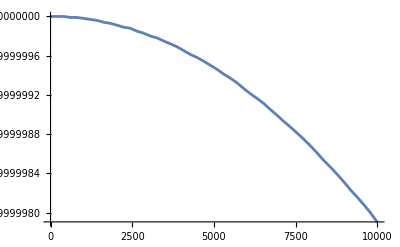

```mathematica
Plot[kd1[x],{x,0.001,10000.}]
```

## Γ = 1 and ρ = ρ_0(1-r/b)

```mathematica
FullSimplify[m'[r]^2 (-16^Γ π^(2 Γ) (r^3 Λ+3 m[r])-3 (4 π)^(1+Γ) r^3 K[r] (m'[r]/r^2)^Γ)-4 π r^4 (m'[r]/r^2)^(1+Γ) (K[r] (-2^(1+2 Γ) π^Γ Γ (3 r+r^3 Λ-6 m[r])+(4 π)^Γ (r^3 Λ+3 m[r]))+r ((4 π)^Γ r (3+r^2 Λ)-3 2^(1+2 Γ) π^Γ m[r]) K'[r]+12 π r^3 K[r]^2 (m'[r]/r^2)^Γ)-4 π r^3 Γ K[r] ((4 π)^Γ r (3+r^2 Λ)-3 2^(1+2 Γ) π^Γ m[r]) (m'[r]/r^2)^Γ m''[r]/.{Γ->1,m[r]->4 Subscript[ρ, 0] π (r^3/3-r^4/(4 b)),m'[r]->4 Subscript[ρ, 0] π (r^2-r^3/b),m''[r]->4 Subscript[ρ, 0] π (2 r-(3 r^2)/b)}]
```

(256 π^4 (b-r) r^6 ρ_0^2 (-12 π (b-r)^2 r K[r]^2 ρ_0+K[r] (b (3-(b-2 r) r Λ)+π r (-16 b^2+23 b r-9 r^2) ρ_0)+(b-r) (-b r Λ-b (3+r^2 Λ) K'[r]+π (4 b-3 r) r ρ_0 (-1+2 r K'[r]))))/b^3

```mathematica
kd2=NDSolveValue[{(-12 π (b-r)^2 r K[r]^2 Subscript[ρ, 0]+K[r] (b (3-(b-2 r) r Λ)+π r (-16 b^2+23 b r-9 r^2) Subscript[ρ, 0])+(b-r) (-b r Λ-b (3+r^2 Λ) K'[r]+π (4 b-3 r) r Subscript[ρ, 0] (-1+2 r K'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},K[0.001]==0.0001},K,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

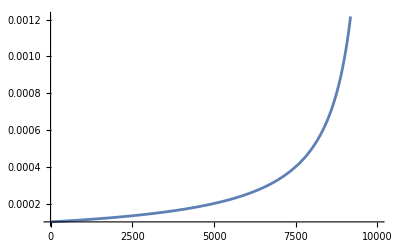

```mathematica
Plot[kd2[r],{r,0,10000}]
```

## Γ = 1 and ρ = ρ_0(1-r^2/b^2)

```mathematica
FullSimplify[m'[r]^2 (-16^Γ π^(2 Γ) (r^3 Λ+3 m[r])-3 (4 π)^(1+Γ) r^3 K[r] (m'[r]/r^2)^Γ)-4 π r^4 (m'[r]/r^2)^(1+Γ) (K[r] (-2^(1+2 Γ) π^Γ Γ (3 r+r^3 Λ-6 m[r])+(4 π)^Γ (r^3 Λ+3 m[r]))+r ((4 π)^Γ r (3+r^2 Λ)-3 2^(1+2 Γ) π^Γ m[r]) K'[r]+12 π r^3 K[r]^2 (m'[r]/r^2)^Γ)-4 π r^3 Γ K[r] ((4 π)^Γ r (3+r^2 Λ)-3 2^(1+2 Γ) π^Γ m[r]) (m'[r]/r^2)^Γ m''[r]/.{Γ->1,m[r]->4 Subscript[ρ, 0] π (r^3/3-r^5/(5 b^2)),m'[r]->4 Subscript[ρ, 0] π (r^2-r^4/b^2),m''[r]->4 Subscript[ρ, 0] π (2 r-(4 r^3)/b^2)}]
```

(256 π^4 (b-r) r^6 (b+r) ρ_0^2 (-60 π r (b^2-r^2)^2 K[r]^2 ρ_0+r K[r] (5 b^2 (6-b^2 Λ+3 r^2 Λ)-8 π (10 b^4-9 b^2 r^2+3 r^4) ρ_0)-(b-r) (b+r) (4 π r (-5 b^2+3 r^2) ρ_0 (-1+2 r K'[r])+5 b^2 (r Λ+(3+r^2 Λ) K'[r]))))/(5 b^6)

```mathematica
kd3=NDSolveValue[{(-60 π r (b^2-r^2)^2 K[r]^2 Subscript[ρ, 0]+r K[r] (5 b^2 (6-b^2 Λ+3 r^2 Λ)-8 π (10 b^4-9 b^2 r^2+3 r^4) Subscript[ρ, 0])-(b-r) (b+r) (4 π r (-5 b^2+3 r^2) Subscript[ρ, 0] (-1+2 r K'[r])+5 b^2 (r Λ+(3+r^2 Λ) K'[r])))==0/.{Λ->10^-52, Subscript[ρ, 0]->10^-22,b->10000},K[0.001]==0.0001},K,{r,0.001,10000}]
```

NDSolveValue::ndsz: At r == 10000., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

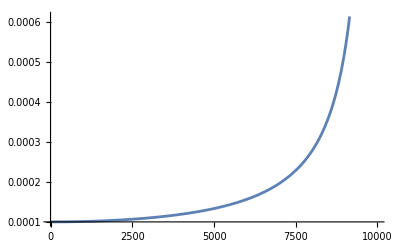

```mathematica
Plot[kd3[r],{r,0,10000}]
```

# Combined Plots

## Density Combined

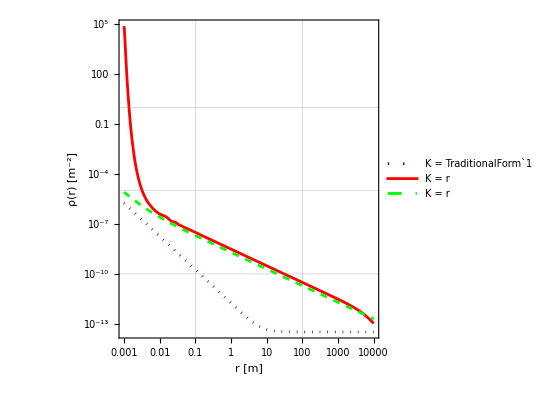

```mathematica
densKas=LogLogPlot[{mp1[r]/(4 π r^2) ,mp2[r]/(4 π r^2) ,mp3[r]/(4 π r^2) },{r,0.001,10000},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain], "ρ(r)"Style["[m^-2]",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = TraditionalForm`1","K = r","K = r"},{Right,Top}],GridLines->Automatic,AspectRatio->1,FrameTicks->{{All,None},{All,None}}]
```

## Γ Combined

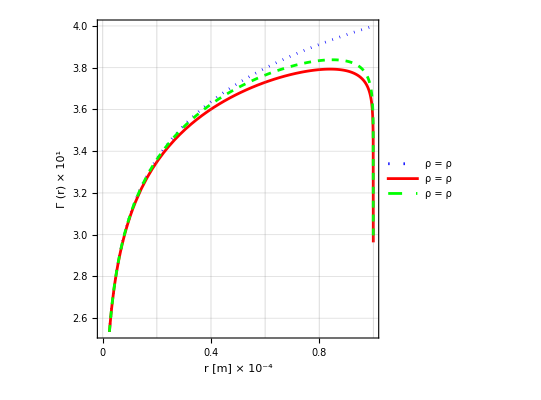

```mathematica
gRhoas=Plot[{gd1[r] 10,gd2[r] 10,gd3[r] 10},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r"  Style["[m]",Plain] Style["× 10^-4",Plain], "Γ"Style["(r)",Plain]  Style["× 10^1",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Right,Bottom}],GridLines->Automatic,AspectRatio->1]
```

## K Combined

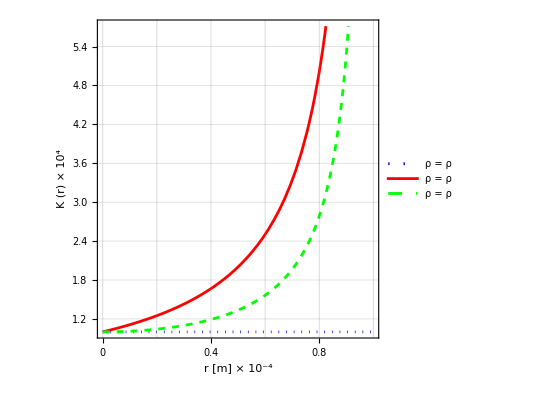

```mathematica
kRhoas=Plot[{kd1[r] 10000,kd2[r] 10000,kd3[r] 10000},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r" Style["[m]",Plain] Style["× 10^-4",Plain], "K"Style["(r)",Plain]  Style["× 10^4",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Top}],GridLines->Automatic,AspectRatio->1]
```

## Pressure Combined

```mathematica
(*We can create a plot for pressure using any of the prior equations and the polytropic EOS. Below is an example using the K[r] plots to make pressure plots*)
```

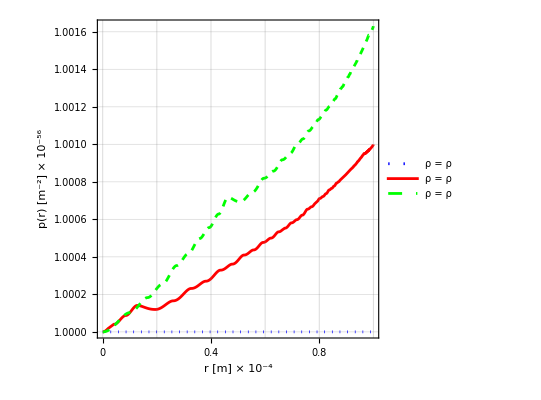

```mathematica
presKRhoas=Plot[{(kd1[r](10^-52))/10^-56,(kd2[r](10^-52)(1 - r/10000))/10^-56,(kd3[r](10^-52)(1 - r^2/10000^2))/10^-56},{r,0.001,10000},FrameTicks->{{Automatic,None},{{{0,"0"},{2000,"0.2"},{4000,"0.4"},{6000,"0.6"},{8000,"0.8"},{10000,"1.0"}},None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r" Style["[m]",Plain] Style["× 10^-4",Plain], "p(r)" Style["[m^-2]",Plain]  Style["× 10^-56",Plain]},PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Left,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
Export["pk.pdf",pk]
```

pk.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["pk.pdf"]]]
```

```mathematica
(*Below is the pressure plot for our Γ plots*)
```

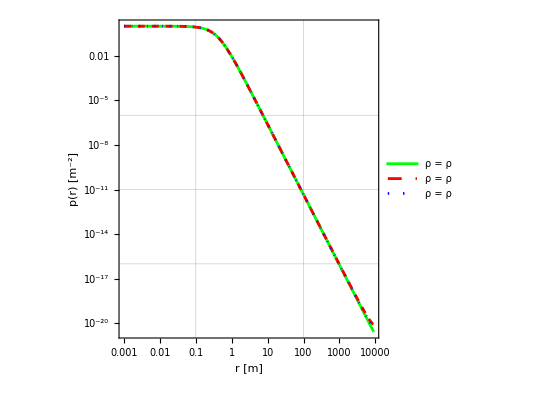

```mathematica
presGRhoas=LogLogPlot[{(10^-52)^gd1[r],((10^-52)(1 - r/10000))^gd2[r] ,((10^-52)(1 - r^2/10000^2))^gd3[r] },{r,0.001,9000},PlotRange->Automatic,Frame->True,FrameLabel->{
"r" Style["[m]",FontSlant->Plain],"p(r)" Style["[m^-2]",Plain]},PlotStyle->{{Green},{Red,Dashed},{Blue,Dotted}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"ρ = ρ","ρ = ρ","ρ = ρ"},{Right,Top}],GridLines->Automatic,AspectRatio->1,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
(*Pressure for second density case. They were plotted seperately due to the difference in values*)
```

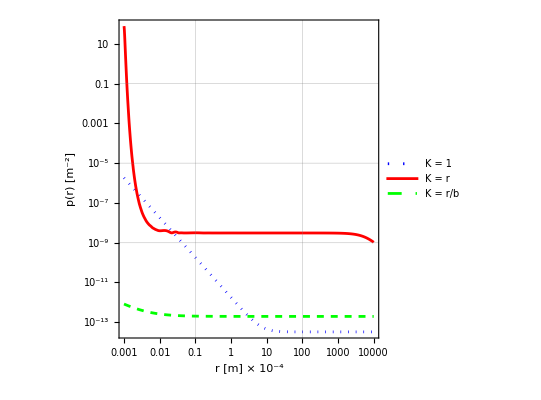

```mathematica
presDenKas=LogLogPlot[{(mp1[r]/(4 π r^2)),(mp2[r]/(4 π r^2))r ,(mp3[r]/(4 π r^2))r/10000},{r,0.001,10000},FrameTicks->{{All,None},{All,None}},PlotRange->Automatic,Frame->True,FrameLabel->{
"r" Style["[m]",Plain] Style["× 10^-4",Plain], "p(r)" Style["[m^-2]",Plain] },PlotStyle->{{Blue,Dotted},{Red},{Green,Dashed}},LabelStyle->Directive[Black, FontFamily->"Palatino Linotype",FontSize->12],PlotLegends->Placed[{"K = 1","K = r","K = r/b"},{Right,Top}],GridLines->Automatic,AspectRatio->1]
```

```mathematica
(*There is not a K=1 and Γ=1 because then the EOS becomes p[r]=ρ[r]*)
```